```mathematica
pathToSolutions=FileNameJoin[{NotebookDirectory[],"dataOut/solutionMatrix.csv"}];
solutions=Import[pathToSolutions,"Table"];
(*pathToEigenvalues=FileNameJoin[{NotebookDirectory[],"dataOut/eigenvalueArray.csv"}];
eigenvalues=Import[pathToEigenvalues,"Table"];*)
```

```mathematica
HarmonicOscillatorψ[n_,x_,m_,ω_,ℏ_]:=((m ω)/(π ℏ))^(1/4)1/(√(2^n n!))HermiteH[n,√((m ω)/ℏ)x] ⅇ^(-(m ω)/(2 ℏ)x^2);
```

```mathematica
Manipulate[
ListLinePlot[solutions[[i]],DataRange->{0,5},PlotRange->Automatic],
{{i,71},1,500,1}
]
```

For N = 750, ρ_max = 5.0

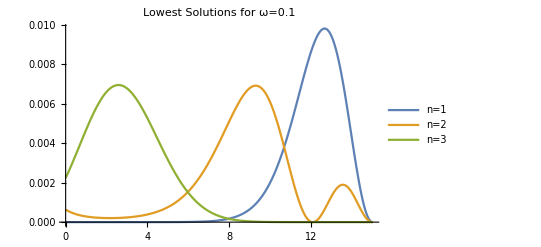

```mathematica
ListLinePlot[Table[solutions[[i]],{i,{172,171,499}}],
DataRange->{0,15},
PlotRange->{{0,15},All},
PlotLegends->{"n=1","n=2","n=3"},
PlotLabel->"Lowest Solutions for ω=0.1",
ImageSize->400
]
```